# Análisis de entropía

## Inicialización

```mathematica
Needs["AdvancedMapping`",FileNameJoin[{ParentDirectory[NotebookDirectory[]],"Extra","AdvancedMapping.wl"}]];
Needs["EconomicComputations`",FileNameJoin[{ParentDirectory[NotebookDirectory[]],"EconomicComputations.wl"}]];

(* Opciones de estilo *)
smallFontSize = 13;
bigFontSize = 15;
plotSize = 500;
colors = {ColorData["Legacy"]["IndianRed"],Black,Blue,ColorData["Legacy"]["Olive"]};
```

### Información de los paquetes cargados

```mathematica
?AdvancedMapping`*
```

```mathematica
?EconomicComputations`*
```

## Cargar base de datos

```mathematica
database = Import[FileNameJoin[{ParentDirectory[NotebookDirectory[]],"Datasets","Prices","DJI_DAX_MXX_NIKKEI_dataset.wdx"}]];
```

## Calculo de entropía continua

```mathematica
HackLog[x_] := If[x>0, Log[x], 0];
ContinuousEntropy[data_]:=Block[{dist},
 dist= SmoothKernelDistribution[data];
-NIntegrate[PDF[dist,x]*HackLog[PDF[dist,x]/PDF[UniformDistribution[{Min[data],Max[data]}],x]],{x,Min[data],Max[data]}]
];
ContinuousEntropySafe[data_]:=Mean@Table[ContinuousEntropy[data],4];
```

```mathematica
market = First[database];
```

```mathematica
ContinuousEntropy[Abs[TrendReturns[market["Prices"]]]]
```

-1.45071

```mathematica
ProgressTable[{database[[i]]["Name"],ContinuousEntropy[Abs[TrendReturns[database[[i]]["Prices"]]]]},{i,1,Length[database]}]
```

{{DAX,-1.45071},{DJIA,-1.68963},{IPC,-1.20152},{NIKKEI225,-1.57514}}

## Sub-optimal trader vs optimal

```mathematica
RandomTradeLengths[maxRun_,totalLength_]:=MapAt[UpTo,NestWhile[Append[#,RandomInteger[{1,maxRun}]]&,{},Total[#]<totalLength&],-1];
RandomLongTradesOverPrices[prices_,maxRun_]:=Returns[Map[First,TakeList[prices,RandomTradeLengths[maxRun,Length[prices]]]]];

LongReturn[{p1_,p2_}]:=Log[p2]-Log[p1];
ShortReturn[{p1_,p2_}]:=Log[p1]-Log[p2];
RandomLongShortTradesOverPrices[prices_,maxRun_]:=Block[{tradePrices,longBuys,shortSales},
tradePrices = Map[First,TakeList[prices,RandomTradeLengths[maxRun,Length[prices]]]];
longBuys = Map[LongReturn,Partition[tradePrices,2,1][[1;;-1;;2]]];
shortSales = Map[ShortReturn,Partition[tradePrices,2,1][[2;;-1;;2]]];

Join[longBuys,shortSales]
];
```

DAX

```mathematica
prices = market["Prices"];
```

```mathematica
randomTrades= ProgressTable[RandomLongShortTradesOverPrices[prices,15],1000];
```

```mathematica
randomTradesEntropies = ProgressParallelMap[ContinuousEntropy,randomTrades];
```

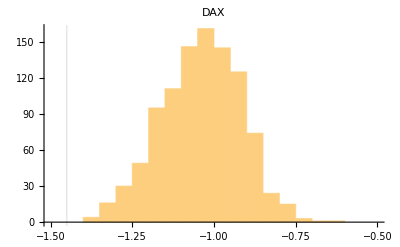

```mathematica
Histogram[randomTradesEntropies,GridLines->{{-1.45},{}},PlotRange->{{-1.5,-0.5},Automatic},PlotLabel->market["Name"]]
```

DJIA

```mathematica
market = database[[2]];
randomTrades= ProgressTable[RandomLongShortTradesOverPrices[market["Prices"],15],1000];
randomTradesEntropies = ProgressParallelMap[ContinuousEntropy,randomTrades];
```

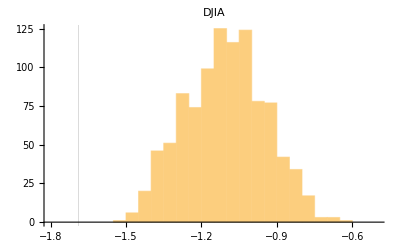

```mathematica
Histogram[randomTradesEntropies,GridLines->{{-1.689},{}},PlotRange->{{-1.8,-0.5},Automatic},PlotLabel->market["Name"]]
```

IPC

```mathematica
market = database[[3]];
randomTrades= ProgressTable[RandomLongShortTradesOverPrices[market["Prices"],15],1000];
randomTradesEntropies = ProgressParallelMap[ContinuousEntropy,randomTrades];
```

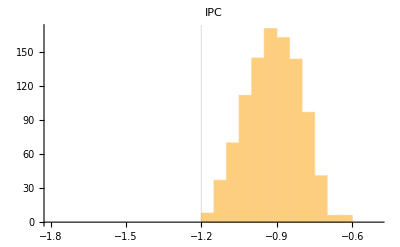

```mathematica
Histogram[randomTradesEntropies,GridLines->{{-1.201},{}},PlotRange->{{-1.8,-0.5},Automatic},PlotLabel->market["Name"]]
```

Nikkei

```mathematica
market = database[[4]];
randomTrades= ProgressTable[RandomLongShortTradesOverPrices[market["Prices"],15],1000];
randomTradesEntropies = ProgressParallelMap[ContinuousEntropy,randomTrades];
```

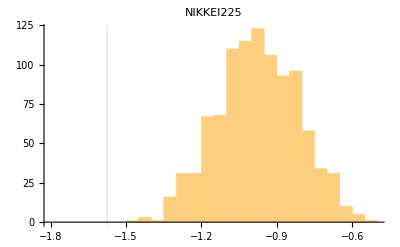

```mathematica
Histogram[randomTradesEntropies,GridLines->{{-1.57514464610976},{}},PlotRange->{{-1.8,-0.5},Automatic},PlotLabel->market["Name"]]
```